```mathematica
Integrate[1/2*(1+m/ϵ)*ϵ/Sqrt[ϵ^2-m^2],ϵ]
```

1/2 (√(-m^2+ϵ^2)+m ArcTanh[ϵ/(√(-m^2+ϵ^2))])

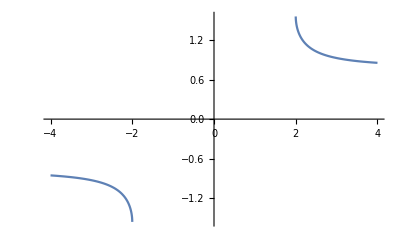

```mathematica
Plot[ArcTan[x/(Sqrt[x^2-4])],{x,-4,4}]
```

```mathematica
SeriesCoefficient[ArcTanh[x/Sqrt[x^2-4]],{x,2,1}]
```

SeriesCoefficient[ArcTanh[x/(√(-4+x^2))],{x,2,1}]

```mathematica
Integrate[1/2*(1+m/ϵ)*ϵ/Sqrt[ϵ^2-m^2]*1/Sqrt[ϵ^2+m^2+Δ^2],ϵ,Assumptions->{Im[m]==0, Re[m]>0, Im[Δ]==0, Re[Δ]>0}]
```

(√(2 m^2+Δ^2) √((m^2+Δ^2+ϵ^2)/(2 m^2+Δ^2)) ArcSinh[(√(-m^2+ϵ^2))/(√(2 m^2+Δ^2))]+(ⅈ √(-1/m^2) m^3 √((m^2+Δ^2+ϵ^2)/(m^2+Δ^2)) √(1-ϵ^2/m^2) EllipticF[ⅈ ArcSinh[√(-1/m^2) ϵ],-m^2/(m^2+Δ^2)])/(√(-m^2+ϵ^2)))/(2 √(m^2+Δ^2+ϵ^2))

```mathematica
Series[s,{ϵ,m,3},Assumptions->{Im[m]==0,Re[m]>0}]
```

1/2 (√2 m+m Log[m+√2 m])+((2+√2) (ϵ-m))/(2 (1+√2))+((-10-7 √2) (ϵ-m)^3)/(48 (1+√2)^3 m^2)+O[ϵ-m]^4

```mathematica
Integrate[((ϵ+m)/(ϵ-m))^(1/2)*1/Sqrt[ϵ^2+4*m^2+Δ^2],ϵ]
```

-((2 (m-ϵ) √(((5 m^2+Δ^2) (m+ϵ))/((3 m^2+Δ^2+2 m √(-4 m^2-Δ^2)) (-m+ϵ))) (-1/(-m+ϵ)2 m (-8 m^3+3 m^2 (√(-4 m^2-Δ^2)+ϵ)+Δ^2 (√(-4 m^2-Δ^2)+ϵ)+2 m (-Δ^2+√(-4 m^2-Δ^2) ϵ)) √((-4 m^3-4 m^2 (√(-4 m^2-Δ^2)-ϵ)+Δ^2 (-√(-4 m^2-Δ^2)+ϵ)-m (Δ^2+√(-4 m^2-Δ^2) ϵ))/((4 m^2+Δ^2) (-m+ϵ))) EllipticF[ArcSin[(√((-m+√(-4 m^2-Δ^2)+(5 m^2)/(m-ϵ)+Δ^2/(m-ϵ))/(√(-4 m^2-Δ^2))))/(√2)],(4 m √(-4 m^2-Δ^2))/(3 m^2+Δ^2+2 m √(-4 m^2-Δ^2))]+√(-4 m^2-Δ^2) (5 m^2+Δ^2) √(((5 m^2+Δ^2) (4 m^2+Δ^2+ϵ^2))/((4 m^2+Δ^2) (m-ϵ)^2)) √((-4 m^3+4 m^2 (√(-4 m^2-Δ^2)+ϵ)+Δ^2 (√(-4 m^2-Δ^2)+ϵ)+m (-Δ^2+√(-4 m^2-Δ^2) ϵ))/((4 m^2+Δ^2) (-m+ϵ))) EllipticPi[(2 √(-4 m^2-Δ^2))/(-m+√(-4 m^2-Δ^2)),ArcSin[(√((-m+√(-4 m^2-Δ^2)+(5 m^2)/(m-ϵ)+Δ^2/(m-ϵ))/(√(-4 m^2-Δ^2))))/(√2)],(4 m √(-4 m^2-Δ^2))/(3 m^2+Δ^2+2 m √(-4 m^2-Δ^2))]))/((5 m^2+Δ^2) (-m+√(-4 m^2-Δ^2)) √((-m+√(-4 m^2-Δ^2)+(5 m^2)/(m-ϵ)+Δ^2/(m-ϵ))/(√(-4 m^2-Δ^2))) √((m+ϵ)/(-m+ϵ)) √(4 m^2+Δ^2+ϵ^2)))

```mathematica
Integrate[((ϵ-m)/(ϵ+m))^(1/2)*1/Sqrt[ϵ^2+4*m^2+Δ^2],ϵ]
```

-1/((m-ϵ) √(4 m^2+Δ^2+ϵ^2))√((-m+ϵ)/(m+ϵ)) √(((5 m^2+Δ^2) (-m+ϵ))/((3 m^2+Δ^2-2 m √(-4 m^2-Δ^2)) (m+ϵ))) (m+ϵ)^2 (1/(√((m+√(-4 m^2-Δ^2)-(5 m^2)/(m+ϵ)-Δ^2/(m+ϵ))/(√(-4 m^2-Δ^2))))4 m (-(m+√(-4 m^2-Δ^2))/(5 m^2+Δ^2)+1/(m+ϵ)) √((-m+√(-4 m^2-Δ^2)+(5 m^2)/(m+ϵ)+Δ^2/(m+ϵ))/(√(-4 m^2-Δ^2))) EllipticF[ArcSin[(√((m+√(-4 m^2-Δ^2)-(5 m^2)/(m+ϵ)-Δ^2/(m+ϵ))/(√(-4 m^2-Δ^2))))/(√2)],-(4 m √(-4 m^2-Δ^2))/(3 m^2+Δ^2-2 m √(-4 m^2-Δ^2))]+1/(m+√(-4 m^2-Δ^2))2 √(-4 m^2-Δ^2) √(((5 m^2+Δ^2) (4 m^2+Δ^2+ϵ^2))/((4 m^2+Δ^2) (m+ϵ)^2)) EllipticPi[(2 √(-4 m^2-Δ^2))/(m+√(-4 m^2-Δ^2)),ArcSin[(√((m+√(-4 m^2-Δ^2)-(5 m^2)/(m+ϵ)-Δ^2/(m+ϵ))/(√(-4 m^2-Δ^2))))/(√2)],-(4 m √(-4 m^2-Δ^2))/(3 m^2+Δ^2-2 m √(-4 m^2-Δ^2))])

```mathematica
Integrate[k/((ξ*k^(2*J)+m^2)^(1/2)),k]
```

(k^2 √(1+(k^(2 J) ξ)/m^2) Hypergeometric2F1[1/2,1/J,1+1/J,-(k^(2 J) ξ)/m^2])/(2 √(m^2+k^(2 J) ξ))

```mathematica
Integrate[k/((ξ*k^(2)+m^2)^(1/2)),k]
```

(√(m^2+k^2 ξ))/ξ

```mathematica
Integrate[k/((ξ*k^(4)+m^2)^(1/2)),k]
```

ArcTanh[(k^2 √ξ)/(√(m^2+k^4 ξ))]/(2 √ξ)

```mathematica
Integrate[k/((ξ*k^(3)+m^2)^(1/2)),k]
```

(k^2 √(1+(k^3 ξ)/m^2) Hypergeometric2F1[1/2,2/3,5/3,-(k^3 ξ)/m^2])/(2 √(m^2+k^3 ξ))

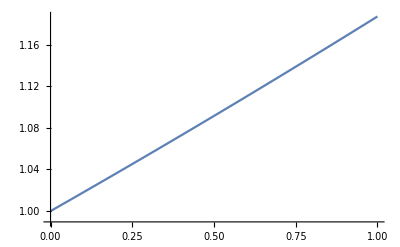

```mathematica
ξ=5;
UA=Table[{m,NIntegrate[(k/2)*(1+m/Sqrt[ξ*k^2+m^2]),{k,0,10}]},{m,0,1,0.01}];
UB=Table[{m,NIntegrate[(k/2)*(1-m/Sqrt[ξ*k^2+m^2]),{k,0,10}]},{m,0,1,0.01}];
RatioAB1=Table[{UA[[i]][[1]],UA[[i]][[2]]/UB[[i]][[2]]},{i,1,Length[UA]}];
ListPlot[RatioAB1,Joined->True]
```

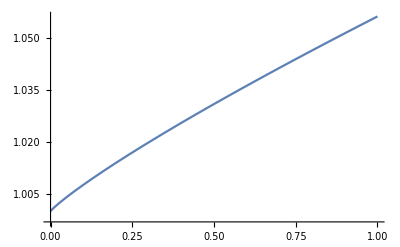

```mathematica
ξ=5;
J=2;
UA=Table[{m,NIntegrate[(k/2)*(1+m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
UB=Table[{m,NIntegrate[(k/2)*(1-m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
RatioAB2=Table[{UA[[i]][[1]],UA[[i]][[2]]/UB[[i]][[2]]},{i,1,Length[UA]}];
ListPlot[RatioAB2,Joined->True]
```

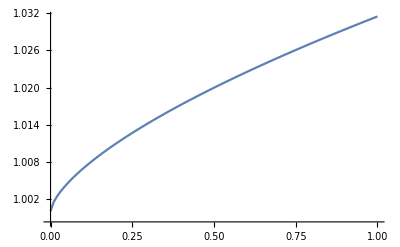

```mathematica
ξ=5;
J=3;
UA=Table[{m,NIntegrate[(k/2)*(1+m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
UB=Table[{m,NIntegrate[(k/2)*(1-m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
RatioAB3=Table[{UA[[i]][[1]],UA[[i]][[2]]/UB[[i]][[2]]},{i,1,Length[UA]}];
ListPlot[RatioAB3,Joined->True]
```

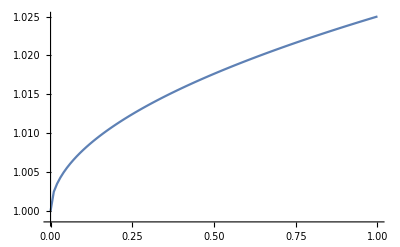

```mathematica
ξ=5;
J=4;
UA=Table[{m,NIntegrate[(k/2)*(1+m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
UB=Table[{m,NIntegrate[(k/2)*(1-m/Sqrt[ξ*k^(2*J)+m^2]),{k,0,10}]},{m,0,1,0.01}];
RatioAB4=Table[{UA[[i]][[1]],UA[[i]][[2]]/UB[[i]][[2]]},{i,1,Length[UA]}];
ListPlot[RatioAB4,Joined->True]
```

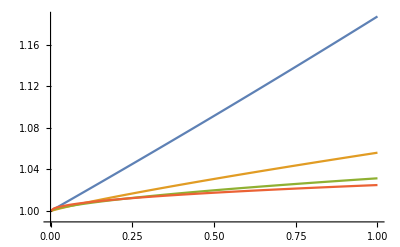

```mathematica
ListPlot[{RatioAB1,RatioAB2,RatioAB3,RatioAB4},Joined->True,PlotRange->All]
```

```mathematica
J=4;
Λ=10;
Ec=Sqrt[Λ^(2*J)+m^2];
Δ=1;
Intplus=Table[{m,NIntegrate[ϵ/(2*Sqrt[ϵ^2-m^2])*(1+m/ϵ)*1/Sqrt[4*ϵ^2+Δ^2],{ϵ,m,Ec}]},{m,0,1,0.01}]
Intminus=Table[{m,NIntegrate[ϵ/(2*Sqrt[ϵ^2-m^2])*(1-m/ϵ)*1/Sqrt[4*ϵ^2+Δ^2],{ϵ,m,Ec}]},{m,0,1,0.01}]
```

{{0.,2.64916},{0.01,2.6756},{0.02,2.695},{0.03,2.71166},{0.04,2.72651},{0.05,2.73997},{0.06,2.7523},{0.07,2.76367},{0.08,2.77419},{0.09,2.78397},{0.1,2.79306},{0.11,2.80154},{0.12,2.80944},{0.13,2.81681},{0.14,2.82368},{0.15,2.83008},{0.16,2.83605},{0.17,2.84161},{0.18,2.84677},{0.19,2.85157},{0.2,2.85602},{0.21,2.86014},{0.22,2.86394},{0.23,2.86745},{0.24,2.87067},{0.25,2.87362},{0.26,2.87632},{0.27,2.87878},{0.28,2.881},{0.29,2.88301},{0.3,2.88481},{0.31,2.88641},{0.32,2.88782},{0.33,2.88906},{0.34,2.89013},{0.35,2.89104},{0.36,2.89179},{0.37,2.8924},{0.38,2.89288},{0.39,2.89323},{0.4,2.89345},{0.41,2.89356},{0.42,2.89356},{0.43,2.89345},{0.44,2.89325},{0.45,2.89296},{0.46,2.89257},{0.47,2.89211},{0.48,2.89156},{0.49,2.89095},{0.5,2.89026},{0.51,2.88951},{0.52,2.88869},{0.53,2.88782},{0.54,2.88689},{0.55,2.88591},{0.56,2.88489},{0.57,2.88381},{0.58,2.8827},{0.59,2.88154},{0.6,2.88035},{0.61,2.87912},{0.62,2.87786},{0.63,2.87656},{0.64,2.87524},{0.65,2.87389},{0.66,2.87252},{0.67,2.87112},{0.68,2.8697},{0.69,2.86826},{0.7,2.8668},{0.71,2.86532},{0.72,2.86383},{0.73,2.86232},{0.74,2.8608},{0.75,2.85926},{0.76,2.85771},{0.77,2.85616},{0.78,2.85459},{0.79,2.85301},{0.8,2.85143},{0.81,2.84984},{0.82,2.84824},{0.83,2.84664},{0.84,2.84503},{0.85,2.84342},{0.86,2.8418},{0.87,2.84018},{0.88,2.83856},{0.89,2.83694},{0.9,2.83531},{0.91,2.83368},{0.92,2.83206},{0.93,2.83043},{0.94,2.8288},{0.95,2.82717},{0.96,2.82555},{0.97,2.82392},{0.98,2.8223},{0.99,2.82068},{1.,2.81906}}

{{0.,2.64916},{0.01,2.62262},{0.02,2.60292},{0.03,2.58576},{0.04,2.57021},{0.05,2.55586},{0.06,2.54244},{0.07,2.5298},{0.08,2.51781},{0.09,2.50638},{0.1,2.49545},{0.11,2.48496},{0.12,2.47488},{0.13,2.46516},{0.14,2.45577},{0.15,2.44669},{0.16,2.43789},{0.17,2.42936},{0.18,2.42108},{0.19,2.41303},{0.2,2.40519},{0.21,2.39757},{0.22,2.39013},{0.23,2.38289},{0.24,2.37581},{0.25,2.36891},{0.26,2.36216},{0.27,2.35557},{0.28,2.34912},{0.29,2.34281},{0.3,2.33664},{0.31,2.33059},{0.32,2.32467},{0.33,2.31886},{0.34,2.31317},{0.35,2.30759},{0.36,2.30211},{0.37,2.29674},{0.38,2.29146},{0.39,2.28628},{0.4,2.28119},{0.41,2.27619},{0.42,2.27128},{0.43,2.26645},{0.44,2.2617},{0.45,2.25703},{0.46,2.25243},{0.47,2.24791},{0.48,2.24346},{0.49,2.23908},{0.5,2.23477},{0.51,2.23052},{0.52,2.22634},{0.53,2.22222},{0.54,2.21816},{0.55,2.21415},{0.56,2.21021},{0.57,2.20632},{0.58,2.20248},{0.59,2.1987},{0.6,2.19497},{0.61,2.19129},{0.62,2.18766},{0.63,2.18407},{0.64,2.18053},{0.65,2.17704},{0.66,2.17359},{0.67,2.17019},{0.68,2.16683},{0.69,2.1635},{0.7,2.16022},{0.71,2.15698},{0.72,2.15378},{0.73,2.15061},{0.74,2.14749},{0.75,2.14439},{0.76,2.14134},{0.77,2.13831},{0.78,2.13533},{0.79,2.13237},{0.8,2.12945},{0.81,2.12656},{0.82,2.1237},{0.83,2.12087},{0.84,2.11807},{0.85,2.1153},{0.86,2.11256},{0.87,2.10984},{0.88,2.10716},{0.89,2.1045},{0.9,2.10187},{0.91,2.09926},{0.92,2.09668},{0.93,2.09412},{0.94,2.09159},{0.95,2.08909},{0.96,2.0866},{0.97,2.08414},{0.98,2.08171},{0.99,2.07929},{1.,2.0769}}

```mathematica
Clear[Δ]
Integrate[Sqrt[(ϵ+m)/(ϵ-m)]*1/Sqrt[4*ϵ^2+Δ^2],ϵ]
Integrate[Sqrt[(ϵ-m)/(ϵ+m)]*1/Sqrt[4*ϵ^2+Δ^2],ϵ]
```

((m+ϵ) ((4 m (2 m-ⅈ Δ) √(((2 m+ⅈ Δ) (Δ+2 ⅈ ϵ))/(Δ (m-ϵ))) (ⅈ Δ+2 ϵ) EllipticF[ArcSin[1/2 √(((2 ⅈ m+Δ) (ⅈ Δ+2 ϵ))/(Δ (-m+ϵ)))],-(8 ⅈ m Δ)/(2 m-ⅈ Δ)^2])/(-m+ϵ)-Δ (-2 ⅈ m+Δ) √(((2 ⅈ m+Δ) (ⅈ Δ+2 ϵ))/(Δ (-m+ϵ))) √(((4 m^2+Δ^2) (Δ^2+4 ϵ^2))/(Δ^2 (m-ϵ)^2)) EllipticPi[-(2 ⅈ Δ)/(2 m-ⅈ Δ),ArcSin[1/2 √(((2 ⅈ m+Δ) (ⅈ Δ+2 ϵ))/(Δ (-m+ϵ)))],-(8 ⅈ m Δ)/(2 m-ⅈ Δ)^2]))/((2 m-ⅈ Δ)^2 √(((2 m+ⅈ Δ) (m+ϵ))/((2 m-ⅈ Δ) (m-ϵ))) √((m+ϵ)/(-m+ϵ)) √(((2 ⅈ m+Δ) (ⅈ Δ+2 ϵ))/(Δ (-m+ϵ))) √(Δ^2+4 ϵ^2))

-((√((-m+ϵ)/(m+ϵ)) (m+ϵ) (-1/(m+ϵ)4 m (2 m-ⅈ Δ) √(((2 m+ⅈ Δ) (Δ-2 ⅈ ϵ))/(Δ (m+ϵ))) (-ⅈ Δ+2 ϵ) EllipticF[ArcSin[1/2 √(((2 m-ⅈ Δ) (Δ+2 ⅈ ϵ))/(Δ (m+ϵ)))],-(8 ⅈ m Δ)/(2 m-ⅈ Δ)^2]+Δ (-2 ⅈ m+Δ) √(((2 m-ⅈ Δ) (Δ+2 ⅈ ϵ))/(Δ (m+ϵ))) √(((4 m^2+Δ^2) (Δ^2+4 ϵ^2))/(Δ^2 (m+ϵ)^2)) EllipticPi[-(2 ⅈ Δ)/(2 m-ⅈ Δ),ArcSin[1/2 √(((2 m-ⅈ Δ) (Δ+2 ⅈ ϵ))/(Δ (m+ϵ)))],-(8 ⅈ m Δ)/(2 m-ⅈ Δ)^2]))/((2 m-ⅈ Δ)^2 √(((2 m+ⅈ Δ) (m-ϵ))/((2 m-ⅈ Δ) (m+ϵ))) √(((2 m-ⅈ Δ) (Δ+2 ⅈ ϵ))/(Δ (m+ϵ))) √(Δ^2+4 ϵ^2)))